## NetSummary & NetSummarize algorithms

### NetSummary:

```mathematica
Clear[NetSummary];
Format[NetSummary[x__, {var_, start_, finish_}]] :=
  DisplayForm[
   RowBox[{UnderoverscriptBox["𝕊", RowBox[{var, "=", start}], finish],
     "[", Sequence @@ Riffle[{x}, ","], "]"}]];
NetSummary /: Expand[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}, {var, start, finish}];
NetSummary /: ExpandAll[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}/.NetSummary[y___]:>Sequence@@(ExpandAll[NetSummary[y]]), {var, start, finish}]
```

### Start of code to summarize Net:

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
FromReducedNetDifferenceSets::usage ="FromNetDifferenceSets[l] unpacks any reduced entries (format n·{…}) in the list l to return a simple list of sets of link lengths for each node of a network.";
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)

FromReducedNetDifferenceSets[ll_List]:=Flatten[ll /.(n_)·l_List :>Sequence@@Table[l,{n}],1]
```

### Primitive Pythagorean Triplets

-Graphics-

#### PPTs

```mathematica
{{3,4,5},{5,12,13}} ~Union~ 
NetSummary[{4n+3,8 n^2+12n+4,8 n^2+12n+5},{4n+4,4 n^2+8n+3,4 n^2+8n+5},
{4n+5,8 n^2+20n+12,8 n^2+20n+13},{n,1,∞}]
```

{{3,4,5},{5,12,13}}∪𝕊_(n=1)^∞[{3+4 n,4+12 n+8 n^2,5+12 n+8 n^2},{4+4 n,3+8 n+4 n^2,5+8 n+4 n^2},{5+4 n,12+20 n+8 n^2,13+20 n+8 n^2}]

```mathematica
{{3,4,5},{5,12,13}} ~Union~ ExpandAll@
NetSummary[{4n+3,8 n^2+12n+4,8 n^2+12n+5},{4n+4,4 n^2+8n+3,4 n^2+8n+5},
{4n+5,8 n^2+20n+12,8 n^2+20n+13},{n,1,5}]
```

{{3,4,5},{5,12,13},{7,24,25},{8,15,17},{9,40,41},{11,60,61},{12,35,37},{13,84,85},{15,112,113},{16,63,65},{17,144,145},{19,180,181},{20,99,101},{21,220,221},{23,264,265},{24,143,145},{25,312,313}}

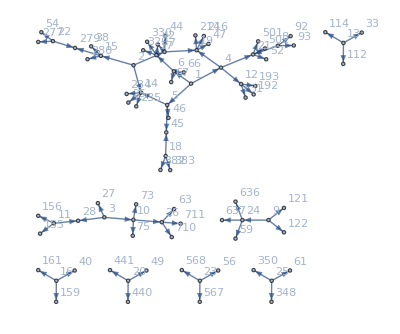

```mathematica
Graph[
FromNetDifferenceSets[{{3,4,5},{5,12,13}} ~Union~ ExpandAll@
NetSummary[{4n+3,8 n^2+12n+4,8 n^2+12n+5},{4n+4,4 n^2+8n+3,4 n^2+8n+5},
{4n+5,8 n^2+20n+12,8 n^2+20n+13},{n,1,8}]],
VertexLabels->"Name"]
```